```mathematica
Remove["Global`*"]
```

Remove::rmnsm: There are no symbols matching "Global`*".

```mathematica
(*Electrostatic potential for a line charge*)
```

```mathematica
k=N[299792458^2*10^-7]                                  
(*k = 1/(4 Subscript[πϵ, 0]) = c^2 Subscript[μ, 0]/(4π)*)
```

8.98755×10^9

```mathematica
U=k*λ*Integrate[1/√(x^2+y^2+(z-w)^2),w]
```

8.98755×10^9 λ Log[w+√(x^2+y^2+(w-z)^2)-z]

```mathematica
Subscript[V, 1][x_,y_,z_]=(U/.{w->.5})-(U/.{w->-.5})                        
(*evaluating indefinite integral first then substituting limits*)
```

-8.98755×10^9 λ Log[-0.5+√(x^2+y^2+(-0.5-z)^2)-z]+8.98755×10^9 λ Log[0.5+√(x^2+y^2+(0.5-z)^2)-z]

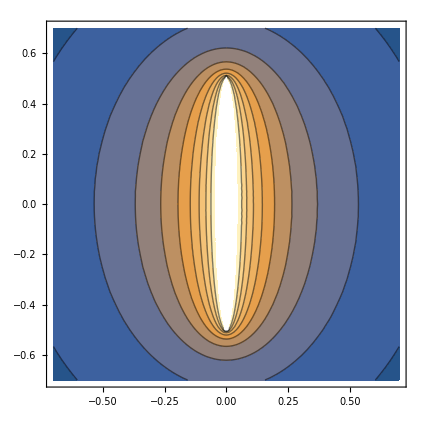

```mathematica
ContourPlot[Subscript[V, 1][x,0,z]/.{λ->1},{x,-.7,.7},{z,-.7,.7}]
```

```mathematica
(*at very close distances the equipotential surfaces are nearly cylindrical and resemble the lines of an infinite line charge. as we move farther away, the finite length of the line charge comes into play, hence the lines bend. at very far distances the lines will become nearly circular, like the equipotentials of a point charge*)
```

```mathematica
(*for λ proportional to z*)
```

```mathematica
Subscript[λ, 2][z_]:=α z
```

```mathematica
ContourPlot[k NIntegrate[(Subscript[λ, 2][w])/(√(x^2+(z-w)^2))/.{α->1},{w,-.5,.5}],{x,-1,1},{z,-1,1}]
```

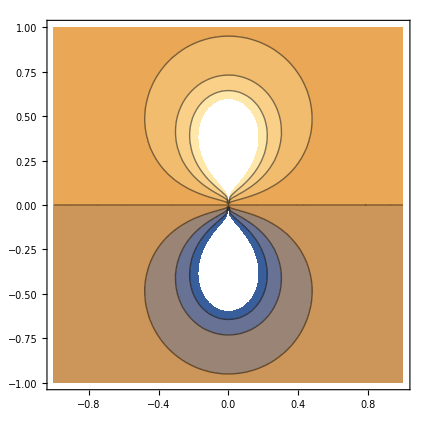

```mathematica
(*using NIntegrate inside ContourPlot command to obtain the equipotential lines*)
```

```mathematica
(*note: this resembles the equipotential lines of a dipole as it contains positive and negative charges. at ∞, it will approach the shape of the equipotential lines of a pure dipole*)
```

```mathematica
(*For λ proportional to ⅇ^(-(z^2/a^2))*)
```

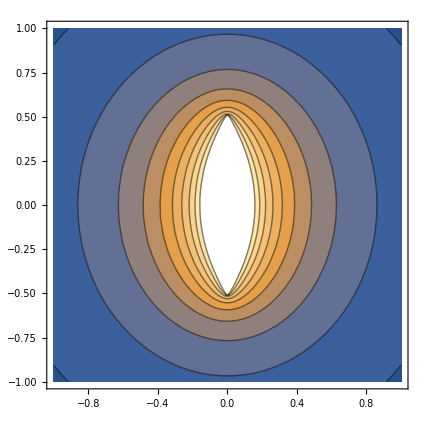
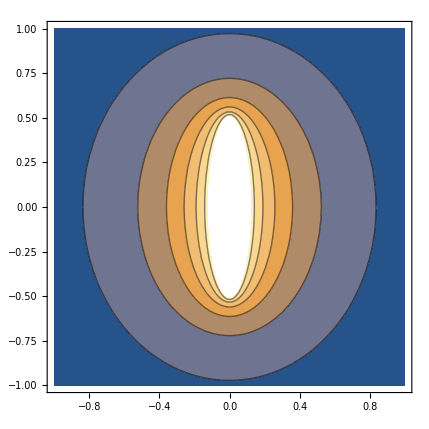

```mathematica
Subscript[λ, 3][z_]:=α ⅇ^(-(z^2/a^2))

Evaluate@Table[ContourPlot[k NIntegrate[(Subscript[λ, 3][w])/(√(x^2+(z-w)^2))/.{α->1},{w,-.5,.5}],{x,-1,1},{z,-1,1}],{a,.5,2,1.5}]
```

```mathematica
(*at large distances the lines will resemble those of a point charge*)
```

```mathematica
(*T/Subscript[T, 0] vs Subscript[A, 0] for a Simple Pendulum*)
```

```mathematica
(*For a simple pendulum which has been displaced by an angle Subscript[A, 0] from its mean position we have from conservation of energy:
KE+PE=constant
initial PE when bob is at rest at its extreme postion= mgh = mgL(1-cos Subscript[A, 0])
														where L is length of pendulum,m its mass and g the gravitational acceleration
Energy at any angle A= 1/2 mv^2+mgh = 1/2 mL^2 ω^2+mgL(1-cos A)
From conservation of energy we have
1/2 mL^2 ω^2+mgL(1-cos A) = mgL(1-cos Subscript[A, 0])
which gives
ω = √(2 g/L(cos A - cos Subscript[A, 0]))= dA/dt
 ∫dt = √(L/(2g))∫dA/(√(cos A - cos Subscript[A, 0]))
one complete time period involves A going from Subscript[A, 0] to (-Subscript[A, 0]) and back again. thus the rhs is 1/4th of the time period if taken from 0 to Subscript[A, 0].
T = 4 √(L/(2g))∫_0^Subscript[A, 0] dA/(√(cos A - cos Subscript[A, 0])) *)
```

```mathematica
Subscript[T, 0]:=2Pi √(L/g)
```

```mathematica
AvsT=Table[{Subscript[A, 0],4 (√(L/(2g)))/Subscript[T, 0] Abs[NIntegrate[1/√(Cos[A]-Cos[Subscript[A, 0]]),{A,0,Subscript[A, 0]}]]},{Subscript[A, 0],-Pi,Pi,Pi/12}]
```

{{-π,24.2075},{-(11 π)/12,2.18544},{-(5 π)/6,1.7622},{-(3 π)/4,1.52795},{-(2 π)/3,1.37288},{-(7 π)/12,1.26221},{-π/2,1.18034},{-(5 π)/12,1.11896},{-π/3,1.07318},{-π/4,1.03997},{-π/6,1.01741},{-π/12,1.0043},{0,0.},{π/12,1.0043},{π/6,1.01741},{π/4,1.03997},{π/3,1.07318},{(5 π)/12,1.11896},{π/2,1.18034},{(7 π)/12,1.26221},{(2 π)/3,1.37288},{(3 π)/4,1.52795},{(5 π)/6,1.7622},{(11 π)/12,2.18544},{π,24.2075}}

```mathematica
(*this is a table of Subscript[A, 0] vs T/Subscript[T, 0] for different Subscript[A, 0] values. we take Abs[] to get positive value *)
```

```mathematica
Show[ListPlot[AvsT],Plot[4 (√(L/(2g)))/Subscript[T, 0] Abs[NIntegrate[1/√(Cos[A]-Cos[Subscript[A, 0]]),{A,0,Subscript[A, 0]}]],{Subscript[A, 0],-Pi,Pi}]]
```

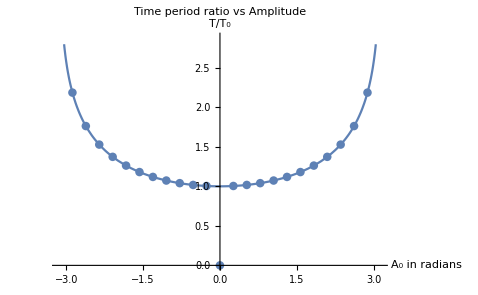

```mathematica
Show[%15,AxesLabel->{HoldForm[Subscript[A, 0] in radians],HoldForm[T/Subscript[T, 0]]},PlotLabel->HoldForm[Time period ratio vs Amplitude],LabelStyle->{GrayLevel[0]}]
```

```mathematica
(*the listplot point for Subscript[A, 0]=0 goes to 0 because the integral limits become 0->0. however, the limit of the function as Subscript[A, 0]->0 is 1*)
```

```mathematica
(*T/Subscript[T, 0] vs Subscript[A, 0] periodic plot, hence plotting from -π to π is sufficient*)
```